## Объявление глобальных переменных

```mathematica
SetDirectory["/Users/kirillivanov/Documents/Code/For Geant analysis/g-xe/"]
print@x_:=(Print@x;x);
grids[dist_]:=Table[If[OddQ@Round@(i/dist),{i,Dashed},{i}],{i,Ceiling@(#1/dist)*dist,Floor@(#2/dist)*dist,dist}]&;
Needs@"ErrorBarPlots`";
dropLastDot@string_:=If[StringTake[string,-1]===".",StringDrop[string,-1],string];
vertSize=0.0001;horizSize=0.0001;
vertCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1+vertSize,#2},{#1-vertSize,#2}}&@@@{coord1,coord2})};
horizCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1,#2+horizSize},{#1,#2-horizSize}}&@@@{coord1,coord2})};
```

/Users/kirillivanov/Documents/Code/For Geant analysis/g-xe

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

## Построение одного графика

### Импорт табличных данных

```mathematica
data = Import["log.csv"];
data//TableForm
```

Energy, MeV | Sigma(E), MeV | E_gap, MeV | Sigma(E_gap), MeV
500. | 0. | 10.8493 | 0.121027
1000. | 0. | 22.8106 | 0.163507
2000. | 0. | 46.686 | 0.248404
3000. | 0. | 70.6841 | 0.289713
4000. | 0. | 94.3525 | 0.349613
5000. | 0. | 118.637 | 0.375965
6000. | 0. | 142.474 | 0.425443
7000. | 0. | 165.472 | 0.441392
8000. | 0. | 189.115 | 0.521443
9000. | 0. | 213.969 | 0.513258
10000. | 0. | 238.317 | 0.487873

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

FittedModel[-0.883488+0.0237577 x+1.17646×10^-8 x^2]

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.883488 | 0.374412 | -2.35967 | 0.0459818
x | 0.0237577 | 0.000173267 | 137.116 | 8.95035×10^-15
x^2 | 1.17646×10^-8 | 1.6334×10^-8 | 0.720254 | 0.491874

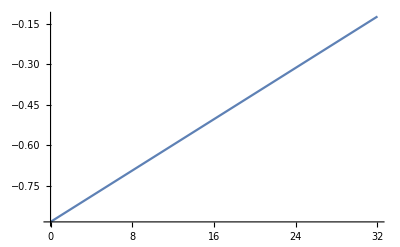

```mathematica
forFit=data⟦2;;,{1,3}⟧;
forFitCr=data⟦2;;,-1⟧;
fit2=LinearModelFit[forFit,{1,x, x^2},x]
fit2@"ParameterTable"
Plot[fit2["Function"]@x, {x, 0, 32}]
```

```mathematica
((print@fit2["FitResiduals"])/(print@forFitCr))^2
χ22=Total[(fit2["FitResiduals"]/forFitCr)^2]/(11-3)
```

{-0.149011,-0.0753811,0.00699499,0.188632,0.0169444,0.438101,0.387979,-0.524605,-0.816345,0.080062,0.446627}

{0.121027,0.163507,0.248404,0.289713,0.349613,0.375965,0.425443,0.441392,0.521443,0.513258,0.487873}

{1.5159,0.212546,0.000792971,0.42393,0.00234897,1.35786,0.831636,1.41259,2.45094,0.0243322,0.838062}

1.13387

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

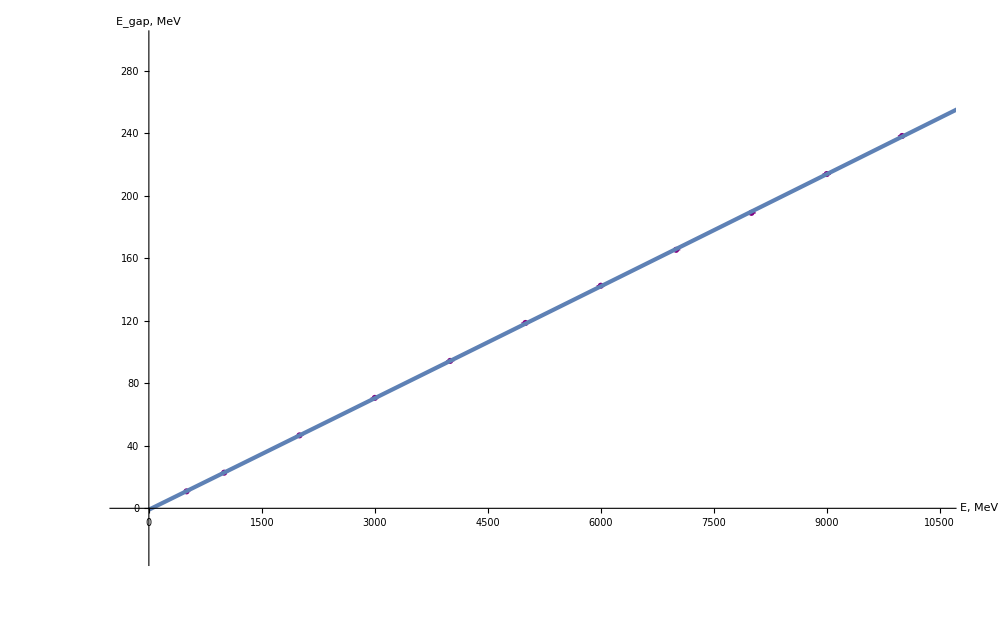

images/png/calib2.png

images/png/fit_res2.png

```mathematica
plot2 =Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@data⟦2;;,{1,3,2,4}⟧,
GridLines->{grids@500,grids@50},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"E, MeV","E_gap, MeV"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.006,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
(*Ticks->{myTicksX,myTicksY},*)
PlotRange->{{-300,10500},{-30,299}}], 
Plot[fit2["Function"]@x,{x,0,10900}, PlotStyle->Thickness@0.003]]
Export["images/png/calib2.png",plot2,"PNG"]
Export["images/png/fit_res2.png",fit2@"ParameterTable","PNG"]
```

#### Экспорт фита данных в CSV формат

```mathematica
exportE = {fit2@"BestFitParameters",fit2@"ParameterErrors",χ22}
Export["fit_res2.csv",exportE,"CSV"]
```

{{-0.883488,0.0237577,1.17646×10^-8},{0.374412,0.000173267,1.6334×10^-8},1.13387}

fit_res2.csv

## Построение одного графика

### Импорт табличных данных

```mathematica
dataR = Import["log_red.csv"];
dataR//TableForm
```

Energy, MeV | Sigma(E), MeV | dE/E | Sigma(dE/E)
850.265 | 8.28338 | 0.239334 | 0.00509072
1370.66 | 11.2364 | 0.196173 | 0.00397175
1966.68 | 12.8344 | 0.162945 | 0.00317074
2952.1 | 15.1665 | 0.133791 | 0.00254132
3564.53 | 18.4525 | 0.125295 | 0.00238114
4151.59 | 18.7812 | 0.116476 | 0.00219549
5029.11 | 21.4641 | 0.102859 | 0.00193262
6342.3 | 23.3313 | 0.0924868 | 0.00172265
7154.24 | 25.882 | 0.0873492 | 0.00162904
7993.13 | 27.7559 | 0.0847265 | 0.00157797
9782.65 | 25.4219 | 0.0785107 | 0.00144784

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

FittedModel[0.00876149+6.81182/(√x)]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.00876149 | 0.00175214 | 5.00046 | 0.000738502
1/(√x) | 6.81182 | 0.0919066 | 74.1168 | 7.49402×10^-14

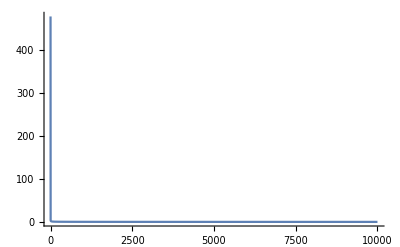

```mathematica
forFitR=dataR⟦2;;,{1,3}⟧;
fitR=LinearModelFit[forFitR,{1,1/Sqrt[x]},x]
forFitCrR=dataR⟦2;;,-1⟧;
fitR@"ParameterTable"
Plot[fitR["Function"]@x, {x, 0, 10000}, PlotRange->All]
```

```mathematica
((print@fitR["FitResiduals"])/(print@forFitCrR))^2
χR=Total[(fitR["FitResiduals"]/forFitCrR)^2]/(11-2)
```

{-0.00303433,0.00342014,0.000582123,-0.000341914,0.00244,0.00199436,-0.00195711,-0.00180884,-0.00194666,-0.000226191,0.000878433}

{0.00509072,0.00397175,0.00317074,0.00254132,0.00238114,0.00219549,0.00193262,0.00172265,0.00162904,0.00157797,0.00144784}

{0.355277,0.741522,0.0337061,0.0181015,1.05005,0.825172,1.02551,1.10258,1.42797,0.0205473,0.368112}

0.774282

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

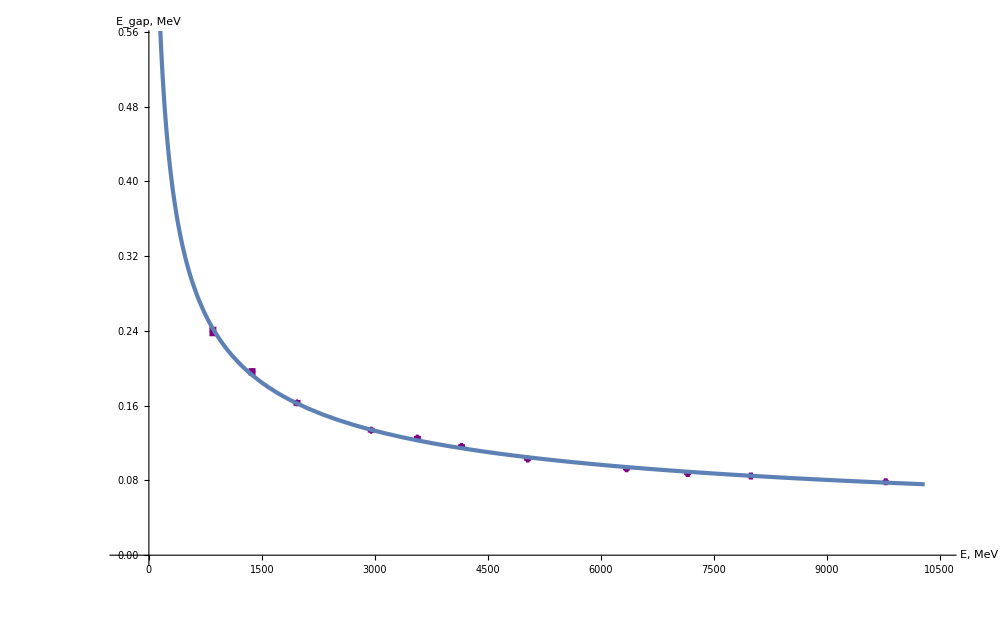

images/png/re.png

images/png/fit_re_res.png

```mathematica
plotR=Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@dataR⟦2;;,{1,3,2,4}⟧,
GridLines->{grids@500,grids@0.05},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"E, MeV","E_gap, MeV"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.005,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
(*Ticks->{myTicksX,myTicksY},*)
PlotRange->{{-300,10500},{0,0.55}}], 
Plot[fitR["Function"]@x,{x,0,10300}, PlotStyle->Thickness@0.003, PlotRange->Full]]
Export["images/png/re.png",plotR,"PNG"]
Export["images/png/fit_re_res.png",fitR@"ParameterTable","PNG"]
```

#### Экспорт фита данных в CSV формат

```mathematica
exportR = {fitR@"BestFitParameters",fitR@"ParameterErrors",χR}
Export["fit_re_res.csv",exportR,"CSV"]
```

{{0.00876149,6.81182},{0.00175214,0.0919066},0.774282}

fit_re_res.csv